```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
mumuraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/firstrun/mumu.dat"];
muaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/firstrun/mua_v2.dat"];
aaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/firstrun/aa.dat"];
```

```mathematica
(*mumuraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/1TeV/mumufortt/oneTeV.dat"];
muaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/1TeV/muafortt/oneTeV_corrected.dat"];
aaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/1TeV/aafortt/oneTeV.dat"];*)
```

```mathematica
mumu=Table[{0.1*2^(i-6),mumuraw[[i,3]]},{i,1,Length[muaraw]}];
mumuerror=Table[{0.1*2^(i-6),mumuraw[[i,4]]},{i,1,Length[muaraw]}];
mua=Table[{0.1*2^(i-6),muaraw[[i,3]]},{i,1,Length[muaraw]}];
muaerror=Table[{0.1*2^(i-6),muaraw[[i,4]]},{i,1,Length[muaraw]}];
aa=Table[{0.1*2^(i-6),aaraw[[i,3]]},{i,1,Length[muaraw]}];
aaerror=Table[{0.1*2^(i-6),aaraw[[i,4]]},{i,1,Length[muaraw]}];
```

```mathematica
Dlog=aa
Slog=coeff[diff[mua,aa],2]
```

{{0.003125,0.025565},{0.00625,0.022629},{0.0125,0.019878},{0.025,0.017301},{0.05,0.014902},{0.1,0.012676},{0.2,0.010626},{0.4,0.0087508},{0.8,0.0070503},{1.6,0.005526},{3.2,0.0041746},{6.4,0.0029962},{12.8,0.0019916}}

{{0.003125,0.0146784},{0.00625,0.0154994},{0.0125,0.0156821},{0.025,0.0153424},{0.05,0.0145676},{0.1,0.0135442},{0.2,0.0123828},{0.4,0.0111001},{0.8,0.0099734},{1.6,0.00857707},{3.2,0.0073871},{6.4,0.00639393},{12.8,0.00530802}}

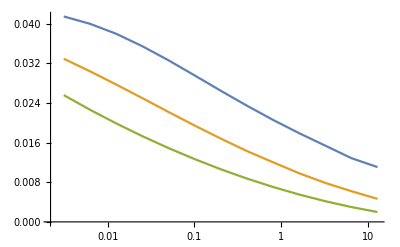

```mathematica
ListLogLinearPlot[{mumu,mua,aa},Joined->True]
```

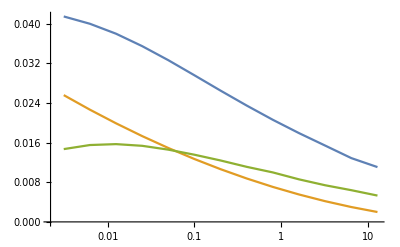

```mathematica
ListLogLinearPlot[{mumu,Dlog,Slog},Joined->True]
```

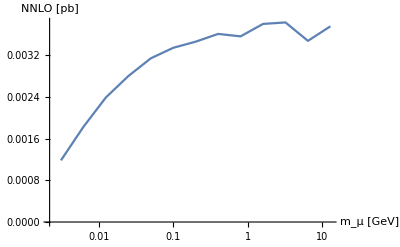

```mathematica
ListLogLinearPlot[diff[diff[mumu,Dlog],Slog],Joined->True,AxesLabel->{"m_μ [GeV]", "NNLO [pb]"}]
```

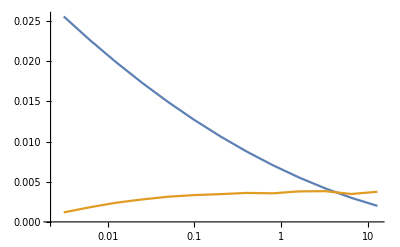

```mathematica
ListLogLinearPlot[{aa,diff[diff[mumu,Dlog],Slog]},Joined->True]
```